```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4,k},
ψ[x_,y_]:=(a1 Exp[I k x]+a2 Exp[-I k x])(a3 Exp[k y]+a4 Exp[-k y]);
FullSimplify[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]]
]
```

0

```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4,b1,b2,b3,b4,k},
ψ[x_,y_]:=(a1 Exp[I k x]+a2 Exp[-I k x]+a3 Exp[k x]+a4 Exp[-k x])(b1 Exp[k y]+b2 Exp[-k y]+b3 Exp[-I k y]+b4 Exp[I k y]);
FullSimplify[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]]
]
```

4 ⅇ^((-1-ⅈ) k (x+y)) (a1 b4 ⅇ^((1+2 ⅈ) k (x+y))+a3 b1 ⅇ^((2+ⅈ) k (x+y))+a1 b3 ⅇ^(k ((1+2 ⅈ) x+y))+a3 b2 ⅇ^((2+ⅈ) k x+ⅈ k y)+a2 ⅇ^(k (x+y)) (b3+b4 ⅇ^(2 ⅈ k y))+a4 ⅇ^(ⅈ k (x+y)) (b2+b1 ⅇ^(2 k y))) k^4

```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4,k},
ψ[x_,y_]:=(a1 Exp[k x]+a2 Exp[-k x])(a3 Exp[I k y]+a4 Exp[-I k y]);
FullSimplify[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]]
]
```

0

```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4,k},
ψ[x_,y_]:=(a1 Exp[k x]+a2 Exp[-k x])(a3 Exp[k y]+a4 Exp[-k y]);
FullSimplify[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]]
]
```

4 ⅇ^(-k (x+y)) (a2+a1 ⅇ^(2 k x)) (a4+a3 ⅇ^(2 k y)) k^4

```mathematica
DSolve[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]==0,ψ[x,y],{x,y}]
```

DSolve[ψ^(0,4)[x,y]+2 ψ^(2,2)[x,y]+ψ^(4,0)[x,y]==0,ψ[x,y],{x,y}]

```mathematica
DSolve[D[ψ[x,y],{x,2}]+D[ψ[x,y],{y,2}]==0,ψ[x,y],{x,y}]
```

{{ψ[x,y]→C[1][ⅈ x+y]+C[2][-ⅈ x+y]}}

```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4},
ψ[x_,y_]:=a1[I x+y]+a2[-I x+y]+a3[I x-y]+a4[-I x-y];
FullSimplify[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]]
]
```

0

```mathematica
Block[
{ψ,x,y,a1,a2,a3,a4},
ψ[x_,y_]:=a1[I x+y]+a2[-I x+y];
FullSimplify[D[ψ[x,y],{x,4}]+D[ψ[x,y],{y,4}]+2D[ψ[x,y],{x,2},{y,2}]]
]
```

0

```mathematica
D[r^2/4(k3+2k4 Log[r/r1]),r]
```

(k4 r)/2+1/2 r (k3+2 k4 Log[r/r1])

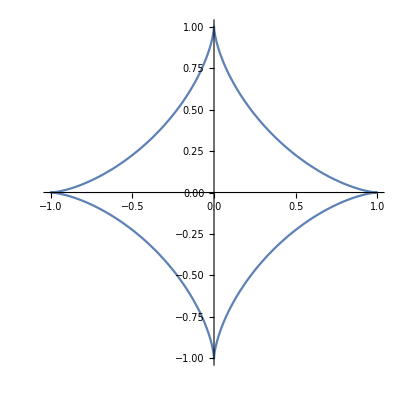

```mathematica
ParametricPlot[{Cos[θ]^3,Sin[θ]^3},{θ,0,2Pi}]
```

```mathematica
Manipulate[
ContourPlot[Abs[x]^(1/n)+Abs[y]^(1/n)==1,{x,-1,1},{y,-1,1}]
,{n,1,2}
]
```

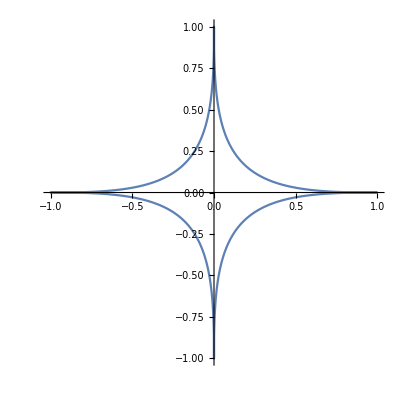

```mathematica
ParametricPlot[{Cos[θ]^5,Sin[θ]^5},{θ,0,2Pi}]
```

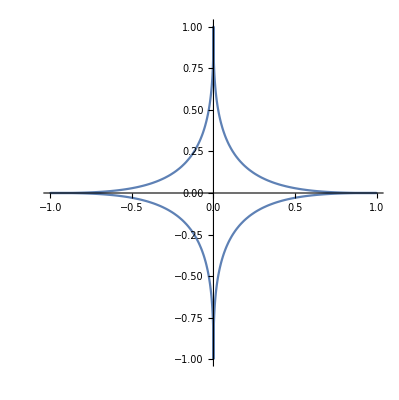

```mathematica
ParametricPlot[{Cos[θ-π/2]^5,Sin[θ-π/2]^5},{θ,0,2Pi}]
```

```mathematica
Manipulate[
ContourPlot[(y-x)^(2/n)+(x+y)^(2/n)==1,{x,-1,1},{y,-1,1}]
,{n,0.25,2}
]
```

```mathematica
Manipulate[
ParametricPlot[{(Cos[θ]^n+Sin[θ]^n)/2,(Cos[θ]^n-Sin[θ]^n)/2},{θ,0,2Pi}]
,{n,1,10}
]
```

```mathematica
Manipulate[
ContourPlot[Abs[x]^(n)+Abs[y]^(n)==1,{x,-1.6,1.6},{y,-1.6,1.6}]
,{n,1,10}
]
```

```mathematica
Manipulate[
ContourPlot[x^(n)+y^(n)==1,{x,-1.6,1.6},{y,-1.6,1.6}]
,{n,1,10}
]
```

```mathematica
Manipulate[
ContourPlot[Abs[x]^(n)+Abs[y]^(n)==r^n,{x,-1,1},{y,-1,1}]
,{n,1,10},{r,0.01,1}
]
```